# NG_4 T_01 ШпакАндрей. Многослойный персептрон

## Замечание. Работа поделена на две части: первая, в которой идет чистовое решение заданий с некоторыми комментариями, и вторая, в которой подробно описан ход мыслей. Я решил сделать именно так, чтобы готовые решения не пришлось искать по всему документу.

1. Искусственная нейросеть и логические операции. Реализуйте три разных нейросети небольшого размера, архитектуры которых приведены на Рис.1. В качестве функции активации используйте пороговую функцию UnitSteppaclet:ref/UnitStep. Математическая модель нейрона (нейросети kmANN21) описывается формулой (DisplayFormulaNumbered).

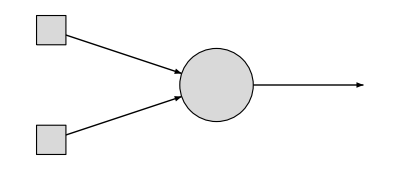
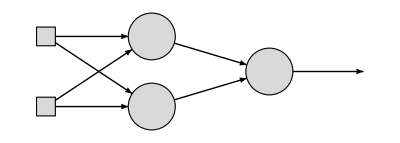
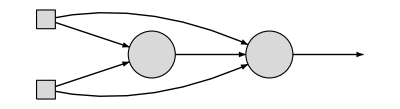
-Graphics-kmANN21 | -Graphics-kmANN221 | -Graphics-kmANN211
Рис 1. Искусственные нейросети

kmANN21_(W⃗)(x⃗):=UnitStep(w_1 x_1+w_2 x_2+w_0)

## Решение:

```mathematica
ClearAll[kmANN21,kmANN221,kmANN211];
kmANN21[W_?VectorQ]@{x1_,x2_}:=UnitStep[W.{x1,x2,1}];
kmANN221[{{W11_,W12_}?MatrixQ,W2_?VectorQ}]@{x1_,x2_}:=UnitStep[W2.{UnitStep[W11.{x1,x2,1}],UnitStep[W12.{x1,x2,1}],1}];
kmANN211[{W1_?VectorQ,W2_?VectorQ}]@{x1_,x2_}:=UnitStep[W2.{x1,UnitStep[W1.{x1,x2,1}],x2,1}]
```

Используя построенные нейросети, реализуем три логических операции: Andpaclet:ref/And, Orpaclet:ref/Or, Xorpaclet:ref/Xor. Для этого подготовим таблицу всевозможных пар логических констант.

```mathematica
BooleDS=Flatten[Table[{x,y},{x,0,1},{y,0,1}],1]
```

{{0,0},{0,1},{1,0},{1,1}}

```mathematica
Do[Print[op,":",Table[StringJoin[ToString[BooleDS[[i]]]," → ",ToString[Boole[op[BooleDS[[i,1]]==1,BooleDS[[i,2]]==1]]]],{i,Length[BooleDS]}]],{op,{And,Or,Xor}}]
```

And:{{0, 0} → 0,{0, 1} → 0,{1, 0} → 0,{1, 1} → 1}

Or:{{0, 0} → 0,{0, 1} → 1,{1, 0} → 1,{1, 1} → 1}

Xor:{{0, 0} → 0,{0, 1} → 1,{1, 0} → 1,{1, 1} → 0}

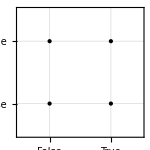

```mathematica
Fig1=Graphics[{PointSize@Medium,Point@BooleDS},ImageSize->150,Frame->True,FrameStyle->Thick,FrameTicks->{#,#}&@{{{0,Style[False,Red]},{1,Style[True,Blue]}},None},PlotRange->{{-.5,1.5},{-.5,1.5}},GridLines->{{0,1},{0,1}}]
```

Операции And и Or реализуйте при помощи одного нейрона — нейросеть kmANN21. Операцию Xor реализуйте двумя способами: при помощи трёх нейронов, расположенных в два слоя — нейросеть kmANN221, и при помощи двух нейронов, расположенных  друг за другом — нейросеть kmANN211 (см. Рис.3).

|  |  | 
Рис 3. Реализация логических операторов искусственными нейросетями

```mathematica
(*Тут мне пришло в голову обратиться к функции UnitStep. Она вернет единичку (истину), если входной аргумент будет ≥ 0. Как же мне достичь такого результата для реализации операции And? Получается, что для ситуаций с {0,0}, {0,1}, {1,0} функция UnitStep должна получать в качестве входного аругмента отрицательное число. А этого можно добиться в случае, если в качестве весов выбрать вектор {1,1,-2}*)
LO=kmAnd=kmANN21[{1,1,-2}]
```

kmANN21[{1,1,-2}]

```mathematica
(*Действительно, получилось:*)
#->LO@#&/@BooleDS
```

{{0,0}→0,{0,1}→0,{1,0}→0,{1,1}→1}

```mathematica
Show[Fig1,DensityPlot[LO@{x1,x2},{x1,-.5,1.5},{x2,-.5,1.5},ColorFunction->(If[#<.1,Opacity[0,Gray],Opacity[.3,Gray]]&)],Graphics[{PointSize@Large,{LO@#/.{0->Red,1->Blue},Point@#}&/@BooleDS}]]
```

-Graphics-

```mathematica
(*Аналогично для Or: выбираю вектор {1,1,-1}:*)
kmOr=kmANN21[{1,1,-1}]
#->kmOr@#&/@BooleDS
```

kmANN21[{1,1,-1}]

{{0,0}→0,{0,1}→1,{1,0}→1,{1,1}→1}

```mathematica
Show[Fig1,DensityPlot[kmOr@{x1,x2},{x1,-.5,1.5},{x2,-.5,1.5},ColorFunction->(If[#<.1,Opacity[0,Gray],Opacity[.3,Gray]]&)],Graphics[{PointSize@Large,{kmOr@#/.{0->Red,1->Blue},Point@#}&/@BooleDS}]]
```

-Graphics-

```mathematica
(*Xor с помощью KmANN221*)
kmXor=kmANN221[{{{1,1,-1},{-1,-1,1}},{1,1,-2}}]
#->kmXor@#&/@BooleDS
```

kmANN221[{{{1,1,-1},{-1,-1,1}},{1,1,-2}}]

{{0,0}→0,{0,1}→1,{1,0}→1,{1,1}→0}

```mathematica
Show[Fig1,DensityPlot[kmXor@{x1,x2},{x1,-.5,1.5},{x2,-.5,1.5},ColorFunction->(If[#<.1,Opacity[0,Gray],Opacity[.3,Gray]]&)],Graphics[{PointSize@Large,{kmXor@#/.{0->Red,1->Blue},Point@#}&/@BooleDS}]]
```

-Graphics-

```mathematica
(*Xor с помощью KmANN211*)
(*Тут еще больше подбор использовал хотя и оглядывался на картинку:*)
```

```mathematica
kmXor=kmANN211[{{1,1,-2},{1,-2,1,-1}}]
#->kmXor@#&/@BooleDS
```

kmANN211[{{1,1,-2},{1,-2,1,-1}}]

{{0,0}→0,{0,1}→1,{1,0}→1,{1,1}→0}

```mathematica
Show[Fig1,DensityPlot[kmXor@{x1,x2},{x1,-.5,1.5},{x2,-.5,1.5},ColorFunction->(If[#<.1,Opacity[0,Gray],Opacity[.3,Gray]]&)],Graphics[{PointSize@Large,{kmXor@#/.{0->Red,1->Blue},Point@#}&/@BooleDS}]]
```

-Graphics-

2. Покрытие области полуплоскостями. В файле «NG23T01Problem.xlsx» на страничке с Вашей фамилией находятся исходные данные, определяющие начертание одной буквы кириллицы. Сама буква находится в первой ячейке первой строки. Вторая ячейка первой строки содержит упакованный рисунок с начертанием данной буквы. Остальные строки содержат координаты угловых точек контура буквы (см. Рис.4). Загрузите свой вариант. Этот и последующие пункты данной работы будут посвящены созданию трёхслойного персептрона, распознающего начертание заданной буквы.

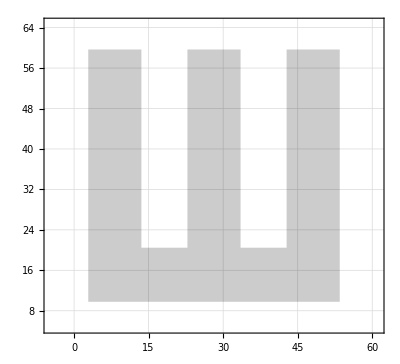
{Ш,-Graphics-,{{2.8512,9.77672},{2.8512,59.6727},{13.5432,59.6727},{13.5432,20.4687},{22.8096,20.4687},{22.8096,59.6727},{33.5016,59.6727},{33.5016,20.4687},{42.768,20.4687},{42.768,59.6727},{53.46,59.6727},{53.46,9.77672}}}

```mathematica
{Letter,FigLetter,Vertices}=Apply[{First@#1,Uncompress@Last@#1,{##2}}&,Import["D:\\neural-networks-tasks\\NG23T01Problem.xlsx",{"Sheets","Шпак Андрей"}]]
```

Начнём с подготовки нейронов первого слоя, каждый из которых будет отвечать за распознавание определённой полуплоскости. Полуплоскость будем задавать парой точек, через которые проходит край полуплоскости. При этом, если двигаться от первой точки ко второй, то сама полуплоскость должна находиться по левую сторону. Используя графический примитив HalfPlanepaclet:ref/HalfPlane, изобразите на рисунке полуплоскость, заданную двумя указанными точками. Для этого для каждой полуплоскости потребуется вычислить нормали к её границе, направленные внутрь этой полуплоскости. Для удобства реализуйте процедуру kmHalfPlane, которая строит полуплоскость по паре граничных точек.

```mathematica
ClearAll[kmHalfPlane];
kmHalfPlane[{P1_,P2_}]:=HalfPlane[]
```

Подготовьте полный список полуплоскостей, из которых в дальнейшем можно будет скомбинировать начертание буквы. Используя оператор Manipulatepaclet:ref/Manipulate, изобразите все выбранные полуплоскости на рисунке (см. Рис.5).

Рис 5. Выбранные полуплоскости

Part::partw: Part {13,12} of {{2.8512,9.77672},{2.8512,59.6727},{13.5432,59.6727},{13.5432,20.4687},{22.8096,20.4687},{22.8096,59.6727},{33.5016,«19»},{33.5016,20.4687},{42.768,20.4687},{42.768,59.6727},{53.46,59.6727},{53.46,9.77672}} does not exist.

Part::partw: Part {20,19} of {{2.8512,9.77672},{2.8512,59.6727},{13.5432,59.6727},{13.5432,20.4687},{22.8096,20.4687},{22.8096,59.6727},{33.5016,«19»},{33.5016,20.4687},{42.768,20.4687},{42.768,59.6727},{53.46,59.6727},{53.46,9.77672}} does not exist.

# Как я разбирался с заданиями

1. Задание.

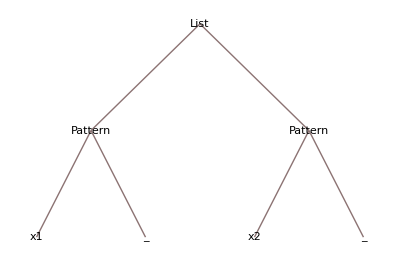

```mathematica
(*Вспоминаю про шаблоны с помощью TreeForm.*)
{x1_,x2_}//TreeForm
```

```mathematica
(*Что такое префикс и для чего он нужен при работе в первом задании. Но так и не понял. ВОПРОС.*)
Prefix[f@{z1, z2}]
```

f@{z1,z2}

```mathematica
{1, 2, 3}*{4,5,6}
```

{4,10,18}

```mathematica
Plus@@({1, 2, 3}*{4,5,6})
```

32

```mathematica
(*Можно и использовать Dot, это более лаконично.*)
{1, 2, 3}.{4,5,6}
```

32

```mathematica
(*Разбираюсь со второй функцией kmANN221.*)
W11={w1,w2}
x1*W11
```

{w1,w2}

{w1 x1,w2 x1}

```mathematica
x1.W11
```

x1.{w1,w2}

```mathematica
const=1
const.{w1,w2}
const.{1,2}
{const, const}.{w1,w2}
```

1

1.{w1,w2}

1.{1,2}

w1+w2

```mathematica
W12={w3,w4}
x1*W11
x2*W12
```

{w3,w4}

{w1 x1,w2 x1}

{w3 x2,w4 x2}

```mathematica
x1*W11[[1]]
x2*W12[[1]]
```

w1 x1

w3 x2

```mathematica
x1*W11[[2]]
x2*W12[[2]]
```

w2 x1

w4 x2

```mathematica
(x1*W11[[1]]).(x2*W12[[1]])
```

(w1 x1).(w3 x2)

```mathematica
(x1*W11[[2]]).(x2*W12[[2]])
```

(w2 x1).(w4 x2)

```mathematica
W2.{(x1*W11[[1]]).(x2*W12[[1]]),(x1*W11[[2]]).(x2*W12[[2]])}
```

Dot::dotsh: Tensors {w3,w4,w5,w0} and {(w1 x1).(w3 x2),(w2 x1).(w4 x2)} have incompatible shapes.

{w3,w4,w5,w0}.{(w1 x1).(w3 x2),(w2 x1).(w4 x2)}

```mathematica
(*Как мне казалось, я сделал правильно, но, пересматривая условие я понял, что сделал не так: забыл про w0 и перепутал весь принцип формирования линейной комбинации значений с весами. Поэтому заново и более внимательно и пошагово ещё раз.*)
```

-Graphics-

```mathematica
W11={w1,w2,w0};
W12={w3,w4,w0};
W11.{x1,x2,1}
W12.{x1,x2,1}
```

w0+w1 x1+w2 x2

w0+w3 x1+w4 x2

```mathematica
W2={w5,w6,w0};
W2.{W11.{x1,x2,1},W12.{x1,x2,1},1}
```

w0+w5 (w0+w1 x1+w2 x2)+w6 (w0+w3 x1+w4 x2)

```mathematica
(*Остается добавить только UnitStep.*)
```

```mathematica
(*Разбираюсь с третьей функцией kmANN211, снова пошагово.*)
-Graphics-
```

-Graphics-

```mathematica
W1={w1,w2,w0};
W2={w3,w4,w5,w0};
W1.{x1,x2,1}
```

w0+w1 x1+w2 x2

```mathematica
W2.{x1,W1.{x1,x2,1},x2,1}
```

w0+w3 x1+w5 x2+w4 (w0+w1 x1+w2 x2)

```mathematica
(*Теперь вспоминаю, как работает Table:*)
BooleDS=Flatten[Table[{x,y},{x,0,1},{y,0,1}],1]
```

{{0,0},{0,1},{1,0},{1,1}}

```mathematica
(*Для начала:*)
Table[x,{x,0,10}]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
Table[{x,y},{x,0,2},{y,0,3}]
(*Получается, что это как список из итераций, где x отвечает за внешний цикл, а y за внутренний.*)
```

{{{0,0},{0,1},{0,2},{0,3}},{{1,0},{1,1},{1,2},{1,3}},{{2,0},{2,1},{2,2},{2,3}}}

```mathematica
(*Теперь Do:*)
Do[Print[BooleDS],{op,{And,Or,Xor}}];
(*Dopaclet:ref/Do[expr,{i,{Subscript[i, 1],Subscript[i, 2],…}}]*)
```

{{0,0},{0,1},{1,0},{1,1}}

{{0,0},{0,1},{1,0},{1,1}}

{{0,0},{0,1},{1,0},{1,1}}

```mathematica
(*Формирование таблицы из операций оказалось сложным после перерыва в использовании вольфрама. Я использовал следующие подходы:*)
```

```mathematica
(*Вспомнил, как работает Part.*)
BooleDS[[1,1]]
```

0

```mathematica
(*And не работал для единиц и нулей, в отличие от своего алиаса.*)
1^1
```

1

```mathematica
(*И я решил это так:*)
And[1==1,1==1]
```

True

```mathematica
(*Составная часть моего списка для каждой из операций можнет выглядеть, например, так (op заменил на And):*)
it=1;
{BooleDS[[it]],Text[" → "],Boole[And[BooleDS[[it,1]]==1,BooleDS[[it,2]]==1]]}
```

{{0,0}, → ,0}

```mathematica
(*Тогда самый простой вариант: Do работает три раза для каждой из операций, значит внутри должен быть еще какой-то цикл для каждого списочка в BooleDS. Но это не совсем то, что нужно.*)
Do[Table[Print[op,Text[": "],BooleDS[[i]]," → ",Boole[op[BooleDS[[i,1]]==1,BooleDS[[i,2]]==1]]],{i,Length[BooleDS]}],{op,{And,Or,Xor}}];
```

And: {0,0} → 0

And: {0,1} → 0

And: {1,0} → 0

And: {1,1} → 1

Or: {0,0} → 0

Or: {0,1} → 1

Or: {1,0} → 1

Or: {1,1} → 1

Xor: {0,0} → 0

Xor: {0,1} → 1

Xor: {1,0} → 1

Xor: {1,1} → 0

```mathematica
(*Точка с запятой разделяет команды им ожно сделать аккуратней, но это все ещё не как в условии:*)
Do[Print[op,Text[": "]];Table[Print[BooleDS[[i]]," → ",Boole[op[BooleDS[[i,1]]==1,BooleDS[[i,2]]==1]]],{i,Length[BooleDS]}],{op,{And,Or,Xor}}];
```

And:

{0,0} → 0

{0,1} → 0

{1,0} → 0

{1,1} → 1

Or:

{0,0} → 0

{0,1} → 1

{1,0} → 1

{1,1} → 1

Xor:

{0,0} → 0

{0,1} → 1

{1,0} → 1

{1,1} → 0

```mathematica
(*А тут все вообще исчезло:*)
Do[Print[op,Text[": "]];Table[{BooleDS[[i]]," → ",Boole[op[BooleDS[[i,1]]==1,BooleDS[[i,2]]==1]]},{i,Length[BooleDS]}],{op,{And,Or,Xor}}]
```

And:

Or:

Xor:

```mathematica
(*Тогда я решил попробовать: что будет, если я сформирую целую строку в Table с помощью функции StringJoin, которую будет выводить Print три раза в Do? Начал с малого, забравшись внуть Table и убрав оттуда Print (op заменил на And):*)
Table[{BooleDS[[i]]," → ",Boole[And[BooleDS[[i,1]]==1,BooleDS[[i,2]]==1]]},{i,Length[BooleDS]}]
```

{{{0,0}, → ,0},{{0,1}, → ,0},{{1,0}, → ,0},{{1,1}, → ,1}}

```mathematica
(*Пробую использовать StringJoin для двух выражений:*)
Table[{StringJoin[ToString[BooleDS[[i]]]," → "],Boole[And[BooleDS[[i,1]]==1,BooleDS[[i,2]]==1]]},{i,Length[BooleDS]}]
```

{{{0, 0} → ,0},{{0, 1} → ,0},{{1, 0} → ,0},{{1, 1} → ,1}}

```mathematica
(*Теперь для целого выражения:*)
Table[StringJoin[ToString[BooleDS[[i]]]," → ",ToString[Boole[And[BooleDS[[i,1]]==1,BooleDS[[i,2]]==1]]]],{i,Length[BooleDS]}]
```

{{0, 0} → 0,{0, 1} → 0,{1, 0} → 0,{1, 1} → 1}

```mathematica
(*Вот и итог:*)
Do[Print[op,":",Table[StringJoin[ToString[BooleDS[[i]]]," → ",ToString[Boole[op[BooleDS[[i,1]]==1,BooleDS[[i,2]]==1]]]],{i,Length[BooleDS]}]],{op,{And,Or,Xor}}]
```

And:{{0, 0} → 0,{0, 1} → 0,{1, 0} → 0,{1, 1} → 1}

Or:{{0, 0} → 0,{0, 1} → 1,{1, 0} → 1,{1, 1} → 1}

Xor:{{0, 0} → 0,{0, 1} → 1,{1, 0} → 1,{1, 1} → 0}

```mathematica
(*Но и этот вариант оказался не совсем правильным ведь я получил выражения, используя строки. Как оказалось, нужно использовать шаблоны, как пример, ячейка ниже. Но переделывать уже не стал.:*)
#->LO@#&/@BooleDS
{{0,0}->0,{0,1}->0,{1,0}->0,{1,1}->1}
```

```mathematica
(*Далее выполнял часть задания с реализацией операций And, Or и Xor. И, если с первыми двумя все было очевидно, то на моменте с реализацией Xor я застопорился. Сначала пробовал подобрать. Не вышло:*)
```

```mathematica
(*В левой части значения, в правой веса*)
{1,0,1}.{1,1,0}
```

1

```mathematica
{1,0,1}.{1,1,-1}
```

0

```mathematica
{1,0,1}.{1,-2,0}
```

1

```mathematica
(**)
```

```mathematica
{0,1,1}.{1,1,0}
```

1

```mathematica
{0,1,1}.{1,1,-1}
```

0

```mathematica
{1,0,1}.{1,-2,0}
```

1

```mathematica
(**)
```

```mathematica
{0,0,1}.{1,1,0}
```

0

```mathematica
{0,0,1}.{1,1,-1}
```

-1

```mathematica
{0,-1,1}.{1,-2,0}
```

2

```mathematica
(**)
```

```mathematica
{1,1,1}.{0,0,1}
```

1

```mathematica
{1,1,1}.{0,0,-1}
```

-1

```mathematica
{1,-1,1}.{1,1,-1}
```

-1

```mathematica
(*В действительности же, забегая наперед, возможно не сразу понятно, что же собственно я пытался подобрать. Но в тот момент я сильно уперся и решил порешать даже неравенства из девяти неизвестных, чтобы найти значения весов, но ничего не считалось в действительных числах, а для комплексных компьютер просто не справлялся.*)
```

```mathematica
Reduce[w7(w1+w3)+w8(w4+w6)+w9≥0&&w7(w2+w3)+w8(w5+w6)+w9≥0&&w7*w3+w8*w6+w9<0&&w7(w1+w2+w3)+w8(w4+w5+w6)+w9<0,{w1,w2,w3,w4,w5,w6,w7,w8,w9},Complexes]
```

Reduce::bdomv: Warning: Complex is not a valid domain specification. Assuming it is a variable to eliminate.

False

```mathematica
Reduce[((w2+w3)w5+w6≥0)&&(w4+(w1+w3)w5+w6≥0)&&(w3*w5+w6<0)&&(w4+(w1+w2+w3)w5+w6<0),{w1,w2,w3,w4,w5,w6},Complexes]
```

{}

```mathematica
Solve[((w2+w3)w5+w6==0)&&(w4+(w1+w3)w5+w6==0)&&(w3*w5+w6==-1),{w1,w2,w3,w4,w5,w6}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{w2→1/w5,w4→1-w1 w5,w6→-1-w3 w5}}

```mathematica
(*Что же я тогда решил? Поискать ответ в интернете! Наткнувшись на видео, я понял, в чем же была проблема...*)
(*Вот это видео: https://www.youtube.com/watch?v=s7nRWh_3BtA&ab_channel=FromLanguagestoInformation*)
(*Проблема была в том, что функции kmANN221 и kmANN211 были реализованы неправильно. Я вообще не обратил внимание, что они сами состоят из нейронов, у которых тоже есть своя функция активации. Итак, я вернулся исправлять самое начало.*)
```

```mathematica
(*Как было:*)
```

```mathematica
ClearAll[kmANN21,kmANN221,kmANN211];
kmANN21[W_?VectorQ]@{x1_,x2_}:=UnitStep[W.{x1,x2,1}];
kmANN221[{{W11_,W12_}?MatrixQ,W2_?VectorQ}]@{x1_,x2_}:=UnitStep[W2.{W11.{x1,x2,1},W12.{x1,x2,1},1}];
kmANN211[{W1_?VectorQ,W2_?VectorQ}]@{x1_,x2_}:=W2.{x1,W1.{x1,x2,1},x2,1}
```

```mathematica
(*Как стало: добавил UnitStep везде, где упустил:*)
```

```mathematica
ClearAll[kmANN21,kmANN221,kmANN211];
kmANN21[W_?VectorQ]@{x1_,x2_}:=UnitStep[W.{x1,x2,1}];
kmANN221[{{W11_,W12_}?MatrixQ,W2_?VectorQ}]@{x1_,x2_}:=UnitStep[W2.{UnitStep[W11.{x1,x2,1}],UnitStep[W12.{x1,x2,1}],1}];
kmANN211[{W1_?VectorQ,W2_?VectorQ}]@{x1_,x2_}:=UnitStep[W2.{x1,UnitStep[W1.{x1,x2,1}],x2,1}]
```

```mathematica
(*Воспользовался этой картинкой, реализовывая операцию Xor, все же подредактировав вектор весов для отрицания And, заменив с (-1,-1,2) на (-1,-1,1):*)
```

2. Задание.

```mathematica
(*Сначала на примере:*)
P1={x1,y1};
P2={x2,y2};
(*Из уравнения прямой по координатам получаю, что*)
(x-P1[[1]])/(P2[[1]]-P1[[1]])
(y-P1[[2]])/(P2[[2]]-P1[[2]])
```

(x-x1)/(-x1+x2)

(y-y1)/(-y1+y2)

```mathematica
(x-P1[[1]])/(P2[[1]]-P1[[1]])*(P2[[2]]-P1[[2]])+P1[[2]]-y==0
(x*P2[[2]]-x*P1[[2]]-P1[[1]]*P2[[2]]+P1[[1]]*P1[[2]])/(P2[[1]]-P1[[1]])+P1[[2]]-y==0
(x*(P2[[2]]-P1[[2]])-P1[[1]]*P2[[2]]+P1[[1]]*P1[[2]])/(P2[[1]]-P1[[1]])+P1[[2]]-y==0
(x*(P2[[2]]-P1[[2]]))/(P2[[1]]-P1[[1]])+(-P1[[1]]*P2[[2]]+P1[[1]]*P1[[2]])/(P2[[1]]-P1[[1]])+P1[[2]]-y==0
```

3-x-y==0

3-x-y==0

3-x-y==0

«1 more identical outputs»

```mathematica
{(P2[[2]]-P1[[2]])/(P2[[1]]-P1[[1]]),-1}
```

{-1,-1}

3-x-y==0

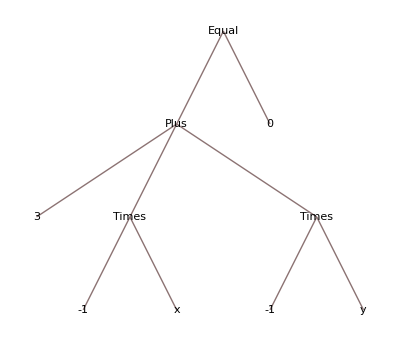

3-x-y==0

```mathematica
(*Проверю с реальными числами:*)
P1={2,1};
P2={1,2};
(x-P1[[1]])/(P2[[1]]-P1[[1]])*(P2[[2]]-P1[[2]])+P1[[2]]-y==0
TreeForm[(x*P2[[2]]-x*P1[[2]]-P1[[1]]*P2[[2]]+P1[[1]]*P1[[2]])/(P2[[1]]-P1[[1]])+P1[[2]]-y==0]
res=(x*P2[[2]]-x*P1[[2]]-P1[[1]]*P2[[2]]+P1[[1]]*P1[[2]])/(P2[[1]]-P1[[1]])+P1[[2]]-y==0
```

```mathematica
(*Реализую и проверяю*)
```

```mathematica
ClearAll[kmHalfPlane];
kmHalfPlane[{P1_,P2_}]:=HalfPlane[{P1,P2},{(P2[[2]]-P1[[2]])/(P2[[1]]-P1[[1]]),-1}]
kmHalfPlane[{P1,P2}]
Graphics[kmHalfPlane[{P1,{1,1}}]]
```

HalfPlane[{{2,1},{1,2}},{-1,-1}]

-Graphics-